## Calculating the center of any geographical region

```mathematica
countryRegion3D[meshI:(_MeshRegion | _BoundaryMeshRegion)]:=
Block[{mesh = Quiet@TriangulateMesh@DiscretizeRegion@meshI},
If[Head[mesh] =!= MeshRegion, Missing[],
MeshRegion[First@GeoPositionXYZ@GeoPosition[Reverse/@
MeshCoordinates[mesh]],MeshCells[mesh,2]]]]
```

```mathematica
regionCenter[r_]:=With[
{pos=GeoPosition@GeoPositionXYZ@RegionCentroid@countryRegion3D@r},
Column@{pos,Hyperlink@StringReplace[
"https://maps.google.com/maps?q=coord&z=5&t=h",
"coord"->pos[[1,;;2]]~StringRiffle~","]}]
```

## I.R. Iran

```mathematica
iran = DiscretizeGraphics[Polygon/@Map[Reverse,
CountryData["Iran", "Polygon"][[1, 1]], {2}]];
countryRegion3D[iran]
```

-Graphics3D-

```mathematica
Head[%]
```

MeshRegion

```mathematica
regionCenter[iran]
```

GeoPosition[{32.5247,54.4659,-25907.}]
https://maps.google.com/maps?q=32.5247,54.4659&z=5&t=h

## Continents

```mathematica
𝕒frica = DiscretizeGraphics[Polygon /@ Map[Reverse,
     (EntityValue[Entity["GeographicRegion", "Africa"], 
        EntityProperty["GeographicRegion", "Polygon"]])[[1, 1]], {2}]];
```

```mathematica
countryRegion3D[𝕒frica]
```

-Graphics3D-

```mathematica
regionCenter@𝕒frica
```

GeoPosition[{6.48893,18.6828,-500164.}]
https://maps.google.com/maps?q=6.48893,18.6828&z=5&t=h

## All the lands in the globe

#### Generate high quality polygons of each region of the world

```mathematica
asia=Polygon/@Map[Reverse,
(EntityValue[Entity["GeographicRegion", "Asia"],
EntityProperty["GeographicRegion", "Polygon"]])[[1, 1]],{2}];
europe=Polygon/@Map[Reverse,
(EntityValue[Entity["GeographicRegion", "Europe"],
EntityProperty["GeographicRegion", "Polygon"]])[[1, 1]],{2}];
africa=Polygon/@Map[Reverse,
(EntityValue[Entity["GeographicRegion", "Africa"],
EntityProperty["GeographicRegion", "Polygon"]])[[1, 1]],{2}];
```

```mathematica
rest=Polygon/@Map[Reverse,
(EntityValue[Entity["GeographicRegion", "World"],
EntityProperty["GeographicRegion", "Polygon"]]//Last//Last)[[1, 1]],
{2}];
```

#### The whole world is a combination of these 3D polygons

```mathematica
world = Union[asia, europe, africa, rest];
```

```mathematica
w = DiscretizeGraphics[world];
```

```mathematica
countryRegion3D[w]
```

-Graphics3D-

```mathematica
regionCenter@w
```

GeoPosition[{44.9857,29.0244,-4.15997×10^6}]
https://maps.google.com/maps?q=44.9857,29.0244&z=5&t=h

## Find the middle-cutting longitude

```mathematica
(*Order of magnitude for number of random points*)
n=10000;
```

```mathematica
points=RandomGeoPosition[Entity["GeographicRegion", "World"],n];
GeoGraphics[{PointSize@.0025,Point@points},GeoProjection->"Mollweide"]
```

-Graphics-

```mathematica
GeoArea@Entity["GeographicRegion", "World"]
```

1.46865×10^8 km^2

```mathematica
(*Get the list of latitudes and longitudes of generated points,
and sort the points by their longitudes*)
info=With[{latlong=points[[1]]},SortBy[
Which[Last@#>180,#-{0,360},
Last@#<-180,#+{0,360},
True,#]&/@latlong,
#[[2]]&]];
```

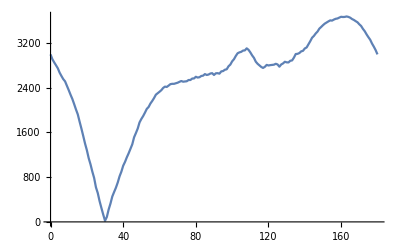

```mathematica
(*Get the east-west-difference of the number of points for each longitude*)
ewd[x_]:=With[{t=CountsBy[info,#[[2]]>x-180&&#[[2]]<=x&]},n-2First@t]
ListPlot[Table[Abs@ewd[x],{x,0,180}],Joined->True,DataRange->{0,180}]
```

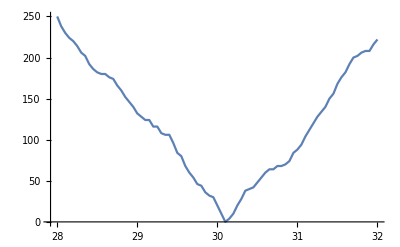

```mathematica
ListPlot[Table[Abs@ewd[x],{x,28,32,.05}],Joined->True,DataRange->{28,32}]
```

### and the middle-cutting latitude

```mathematica
lat=With[{latlong=points[[1]]},SortBy[latlong,#[[1]]&]];
```

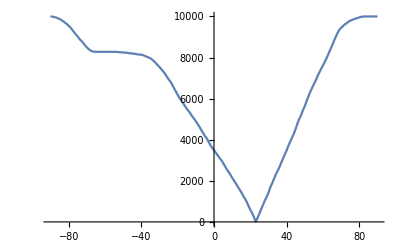

```mathematica
(*Get the north-south-difference of the number of points for each latitude*)
nsd[x_]:=With[{t=CountsBy[lat,#[[1]]>x&]},n-2First@t]
ListPlot[Table[Abs@nsd[x],{x,-90,90}],Joined->True,DataRange->{-90,90}]
```

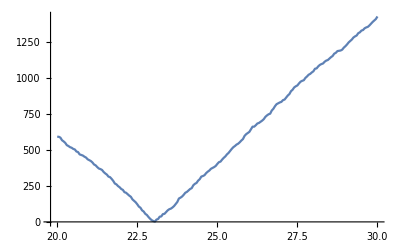

```mathematica
ListPlot[Table[Abs@nsd[x],{x,20,30,.05}],Joined->True,DataRange->{20,30}]
```